```mathematica
ResourceFunction["MaTeXInstall"][]
```

ResourceObject::cloudc: You must connect to the Wolfram cloud to access the resource.

$Failed[]

```mathematica
Needs["PacletManager`"]
```

```mathematica
PacletInstall["/home/maksim/Downloads/MaTeX-1.7.5.paclet"]
```

Paclet[MaTeX,1.7.5,<>]

```mathematica
<<MaTeX`
```

```mathematica
MaTeX["x^2+y^4=1",Magnification->2]
```

-Graphics-

```mathematica
Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
ArrayReshape[Alphabet[][[;;6]],{2,3}]~Join~{{g,h,i}}
```

## Brownian Motion

A standard Brownian motion, or standard Wiener process, over [0,T]  is a random variable W_t that satisfies three properties:

W_0=0 with probability 1

For 0≤s<t≤T it’s the case that W_t - W_s ~ N(0,t-s) ~ √(t-s)N(0,1)

For 0≤s<t<u<v≤T the increments  W_t-W_s and W_u-W_v are independent

Consider discretized Brownian motion: let δt=T/N and j·δt. Conditions 2 and 3 imply

W_j=W_(j-1)+ⅆ W_j

where each ⅆW_j~√δtN(0,1).

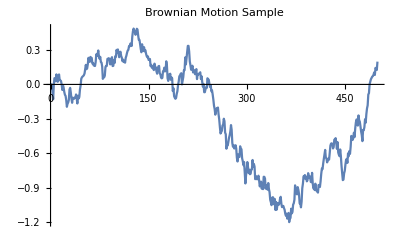

```mathematica
ND :=RandomVariate[NormalDistribution[]];
T=1;n=500;δt=T/n;
dW = ConstantArray[0,n];
W=ConstantArray[0,n];
W[[1]]=√δt ND;
For[j=2,j≤n,j++,
	dW=√δt ND;
	W[[j]]=W[[j-1]]+dW;
];

ListLinePlot[W, PlotLabel->"Brownian Motion Sample"]
```

Vectorized calculations

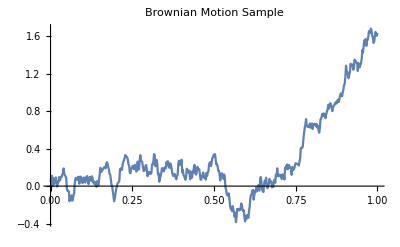

```mathematica
dW = √δt RandomVariate[NormalDistribution[],n];
W=Accumulate[dW];
ListLinePlot[MapThread[{#1,#2}&,{Array[#&,n,{0,T}], W}], PlotLabel->"Brownian Motion Sample"]
```

```mathematica
W//MatrixForm
```

```mathematica
M=1000;
dW = √δt RandomVariate[NormalDistribution[],{n,M}];
dts=Array[#&,n,{0,T}];
(*W=Accumulate[{Table[0,M]}~Join~dW[[2;;-1]]];*)
W=Accumulate[dW];
m=Mean[W//Transpose];
```

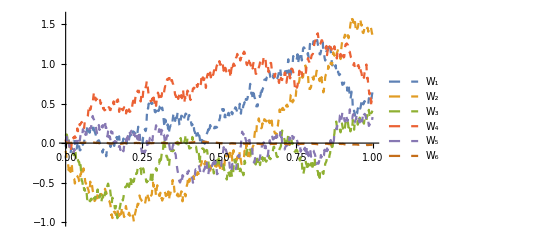

```mathematica
plots = MapThread[Function[{p2,p3},{p2,p3}],{dts,#1}]& /@ ((W[[All,1;;5]]//Transpose)~Join~{m});

labels = Table[Subscript["W", i],{i,M}]~Join~{"mean"};
plotStyles = Table[Dashed,M]~Join~{{Thick,Red}};

ListLinePlot[plots,PlotLegends->labels, PlotStyle->plotStyles]
```

u(W_t)=e^(t+1/2 W_t)

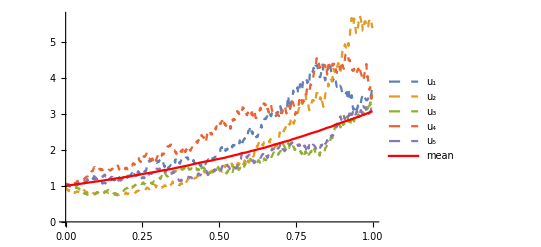

```mathematica
repDts=Table[dts,(W//Dimensions)[[2]]]//Transpose;
u=Exp[repDts+1/2 W];
m=Mean[u//Transpose];

labels = Table[Subscript["u", i],{i,5}]~Join~{"mean"};
plotStyles = Table[Dashed,5]~Join~{{Thick,Red}};

plots = MapThread[Function[{p2,p3},{p2,p3}],{dts,#1}]& /@ (u[[All,1;;5]]//Transpose)~Join~{m};

ListLinePlot[plots,PlotLegends->labels,PlotStyle->plotStyles]
```

Notice that while each individual u_t is non-differentiable the mean is. Indeed it turns out that u_t=e^(9/8 t).

## Stochastic Integrals

Given a suitable function h, the integral ∫_0^T h(t)ⅆt maybe approximated by the Riemann sum
							∑_(j=0)^(N-1) h(t_j)(t_(j+1)-t_j)

where t_j=j δt. In fact the integral is defined as the limit as δt→0 . Similarly
							∑_(j=0)^(N-1) h(t_j)(W_(t_(j+1))-W_t_j)	
can be used to define the Ito Integral ∫_0^T h(t)ⅆ W_t.

Letting h(t)=W_t and recall that W_(j+1)=W_j+ⅆ W_(j+1) (i.e. W_(j+1)-W_j=ⅆ W_(j+1)) we have that 
∫_0^T h(t)ⅆ W_t=lim_(δt→0) ∑_(j=0)^(N-1) W_t_j ⅆ W_(j+1)

```mathematica
dW=√δt*RandomVariate[NormalDistribution[],n];
```

```mathematica
W={0}~Join~Accumulate[dW];
```

```mathematica
ito=Total[W[[;;-2]]*dW]
```

-0.383842

Notice that the Ito integral samples h(t) at the left-hand side of the partition interval (i.e. t_j). An alternative definition is

∑_(j=0)^(N-1) h((t_(j+1)+t_j)/2)(W_(t_j+1)-W_t_j)

This is the Stratonovich integral. Note that this requires having access to h at (t_(j+1)+t_j)/2. In the case where h(t):=W_t it’s the case that

W_((t_(j+1)+t_j)/2)~(W_(t_(j+1))+W_t_j)/2+N(0,δt/4)

```mathematica
dW=√δt*RandomVariate[NormalDistribution[],n];
```

```mathematica
W=Accumulate[dW];
```

```mathematica
h=1/2({0}~Join~W[[;;-2]]+W)+RandomVariate[NormalDistribution[0,δt/4],n];
```

```mathematica
strat=Total[h*dW]
```

0.117338

It’s possible to analytically evaluate these integrals:

∑_(j=0)^(N-1) W_t_j(W_(t_(j+1))-W_t_j)=1/2∑_(j=0)^(N-1) ((W_(t_(j+1)))^2-(W_t_j)^2-(W_(t_(j+1))-W_t_j)^2)
				=1/2(W_T^2-W_0^2-∑_(j=0)^(N-1) (W_(t_(j+1))-W_t_j)^2)

Now E(∑_(j=0)^(N-1) (W_(t_(j+1))-W_t_j)^2)=T and has variance O(δt) hence as δt→0 we have

∑_(j=0)^(N-1) W_t_j(W_(t_(j+1))-W_t_j)→1/2 W_T^2-1/2 T

```mathematica
itoerr = Abs[(1/2(W[[-1]]^2-1))-ito]
```

0.00156346

For the Stratonovich integral we have

∑_(j=0)^(N-1) ((W_(t_(j+1))-W_t_j)/2+Z_j)(W_(t_(j+1))-W_t_j)

where Z_j~N(0,δt/4). There

∑_(j=0)^(N-1) ((W_(t_(j+1))-W_t_j)/2+Z_j)(W_(t_(j+1))-W_t_j)=1/2(W_T^2-W_0^2)+∑_(j=0)^(N-1) Z_j(W_(t_(j+1))-W_t_j)

Since ∑_(j=0)^(N-1) Z_j(W_(t_(j+1))-W_t_j) has expectation 0 and variance O(δt) the Stratonovich integral converges to 1/2 W_T^2

```mathematica
straterr=Abs[1/2 W[[-1]]^2-strat]
```

0.000383063

## Eurler-Maruyama Method

A scalar time-invariant SDE can be written

X_t=X_0+∫_0^t f(X_s)ⅆs+∫_0^t g(X_s)ⅆ W_s

The corresponding differential form is

ⅆX_t=f(X_t)ⅆt+g(X_t)ⅆ W_t

To apply numerical methods first discretize [0,T] using Δt=T/L for some positive integer L, and then τ_j=j Δt. Define X_j:=X_τ_j. The Euler-Maruyama (EM) method takes the form

X_j=X_(j-1)+f(X_(j-1))Δt+g(X_(j-1))(W_j-W_(j-1))

We use this method to linear SDE

ⅆX_t=λ X_t ⅆt+μ X_t ⅆ W_t

i.e. f(X)=λ X and g(X)=μ X. This SDE can be used to derive Black-Scholes and has the exact solution

X_t=X_0 exp((λ+1/2 μ^2)t+μ W_t)

Let λ=2, μ=1, X_0=1. Discretize the Brownian motion over [0,1] with δt=2^-8 and the process step as Δt=R δt where R=4. For an arbitrary step the EM method requires W_τ_j-W_(τ_(j-1)) which is

W_τ_j-W_(τ_(j-1))=W_(j R δt)-W_((j-1)R δt)=∑_(k=(j-1)R+1)^(j R) ⅆ W_k

```mathematica
T=1;n=5000;
```

```mathematica
δt=1/n;λ=2;μ=1;Subscript[X, 0]=1;
```

```mathematica
δts=Array[#&,n,{δt,T}];
```

```mathematica
dW=√δt*RandomVariate[NormalDistribution[], n];
```

```mathematica
W=Accumulate[dW];
```

```mathematica
Subscript[X, true]=Subscript[X, 0] Exp[(λ-1/2 μ^2)δts+μ W];
```

```mathematica
R=4;Δt=R*δt;L=n/R;
```

```mathematica
Xem=Table[0,L];
```

```mathematica
Subscript[X, temp]=Subscript[X, 0];
```

```mathematica
For[j=1,j≤L,j++,
	Subscript[W, inc]=Total[dW[[R (j-1)+1;;R j]]];
	Subscript[X, temp]=Subscript[X, temp]+Δt λ Subscript[X, temp]+μ Subscript[X, temp] Subscript[W, inc];
	Xem[[j]]=Subscript[X, temp];
]
```

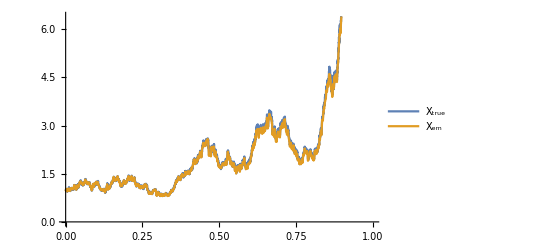

```mathematica
ListLinePlot[{
MapThread[{#1,#2}&,{Array[#&,n,{0,T}], Subscript[X, true]}],
MapThread[{#1,#2}&,{Array[#&,n/R,{0,T}], Xem}]
},PlotLegends->{"X_true","X_em"}]
```

## Strong and Weak Convergence of the EM Method

A method is said to have strong order of convergence equal to γ if there exists C such that

E(|X_n-X_τ|)≤C (Δt)^γ

for any τ=n Δt∈[0,T] and Δt sufficiently small. If f,g satisfy appropriate conditions EM can be shown to be strong order of convergence γ=1/2. In our numerical tests we focus on t=T, so let

e_Δt^strong:=E(|X_L-X_T|) where L Δt=T

```mathematica
If
```